```mathematica
SetDirectory[NotebookDirectory[]];
```

## Fluctuating Temp

```mathematica
ComputeError[dataMom_,dataDVM_,valuesHermite_,PX_]:=Module[{error,qweights,valueMomf},
qweights = dataDVM⟦3,All⟧/f0[dataDVM⟦2,All⟧];

(*value of moment f at the quadrature points*)
valueMomf = valuesHermite⟦All,1;;Length[dataMom]-1⟧.dataMom⟦2;;-1,All⟧;

(*value of error at the quadrature points*)
error = Power[(dataDVM⟦4;;-1,All⟧-valueMomf),2];

(*integrate in the velocity space*)
error=Table[qweights.error⟦All,ii⟧,{ii,1,Length[error⟦1⟧]}];

error = Sqrt[error.PX.error]

]

ComputeDXMomDVM[dataDVM_,valuesHermite_,PX_,DX_]:=Module[{magnitude,qweights,valueDVMom,tempvaluesHermite},

qweights = dataDVM⟦3,All⟧;

tempvaluesHermite = Transpose[valuesHermite];


tempvaluesHermite = Table[ii*qweights,{ii,tempvaluesHermite}];

(*value of moments of the DVM solution*)
valueDVMom = tempvaluesHermite.dataDVM⟦4;;-1,All⟧;


(*derivatives of the moments of the DVM solution*)
valueDVMom = Transpose[DX.Transpose[valueDVMom]];

(*norm of the derivatives*)
magnitude = Table[Sqrt[ii.PX.ii],{ii,valueDVMom}]


]

ComputeDXMom[dataMom_,PX_,DX_]:=Module[{magnitude,qweights,valueDVMom,tempvaluesHermite},

(*derivatives of the moments of the DVM solution*)
valueDVMom = Transpose[DX.Transpose[dataMom]];

(*norm of the derivatives*)
magnitude = Table[Sqrt[ii.PX.ii],{ii,valueDVMom}]


]
```

### Compare refined DVM and Mom

```mathematica
maxDegree = 199;
```

```mathematica
resultDVM = Import["../result_Inflow_fluctuateT_1x1v/DVM_f_inflow_1_points_300_neqn_50.txt","Table"];

resultMom = Import["../result_Inflow_fluctuateT_1x1v/inflow_tend_1_points_300_neqn_200.txt","Table"];
```

```mathematica
vPoints = resultDVM⟦2⟧;
xPoints = resultDVM⟦1⟧;
```

```mathematica
valueHermite = Table[Table[H[jj,ii]*f0[ii],{jj,0,maxDegree}],{ii,vPoints}];
valueMomf = valueHermite.resultMom⟦2;;-1,All⟧;
```

```mathematica
dataMom = Flatten[Table[Table[{xPoints⟦ii⟧,vPoints⟦jj⟧,valueMomf⟦jj,ii⟧},{jj,1,Length[vPoints]}],{ii,1,Length[xPoints]}],1];

dataDVM= Flatten[Table[Table[{xPoints⟦ii⟧,vPoints⟦jj⟧,resultDVM⟦jj+3,ii⟧},{jj,1,Length[vPoints]}],{ii,1,Length[xPoints]}],1];

error = Flatten[Table[Table[{xPoints⟦ii⟧,vPoints⟦jj⟧,Log10[Abs[valueMomf⟦jj,ii⟧-resultDVM⟦jj+3,ii⟧]]},{jj,1,Length[vPoints]}],{ii,1,Length[xPoints]}],1];
```

```mathematica
ListPlot3D[dataMom,PlotRange->Full]
```

```mathematica
ListPlot3D[dataDVM,PlotRange->Full]
```

```mathematica
ListPlot3D[error,PlotRange->Full]
```

### Convergence with respect to DVM

```mathematica
Pmat = Import["../result_Inflow_fluctuateT_1x1v/PX.txt","Table"];
Dmat = Import["../result_Inflow_fluctuateT_1x1v/DX.txt","Table"];
```

```mathematica
Mvalues = Range[4,25,1];
Do[result[ii]=Import[StringJoin["../result_Inflow_fluctuateT_1x1v/inflow_tend_1_points_300_neqn_",ToString[ii],".txt"],"Table"];,{ii,Mvalues}];
```

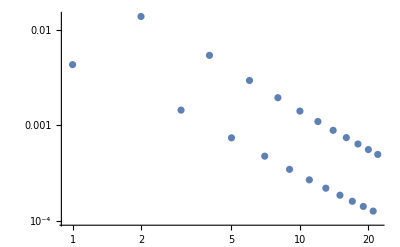

```mathematica
ListLogLogPlot[Table[ComputeError[result[ii],resultDVM,valueHermite,Pmat],{ii,Mvalues}]]
```

```mathematica
magMomenstDVM = ComputeDXMomDVM[resultDVM,valueHermite,Pmat,Dmat];
```

```mathematica
Log10[magMomenstDVM⟦-2⟧/magMomenstDVM⟦-4⟧]/Log10[198/196]
```

-0.829196

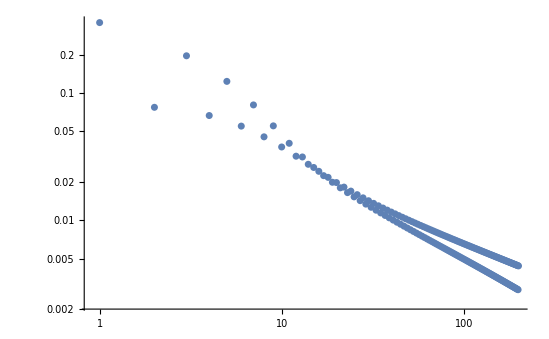

```mathematica
ListLogLogPlot[ComputeDXMomDVM[resultDVM,valueHermite,Pmat,Dmat]]
```

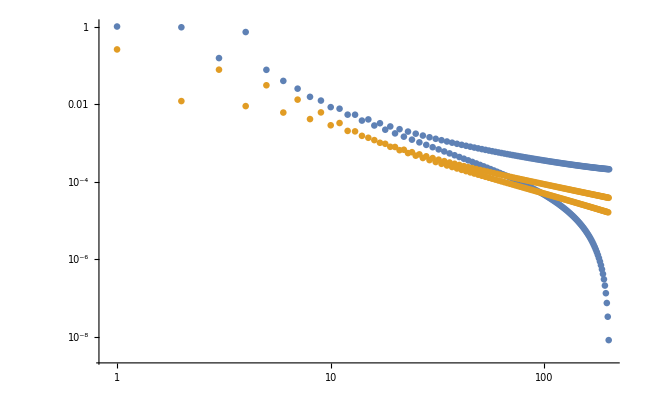

```mathematica
ListLogLogPlot[{ComputeDXMom[resultMom,Pmat,Dmat],ComputeDXMomDVM[resultDVM,valueHermite,Pmat,Dmat]*10/5}]
```

```mathematica
Export["valuesHermite.txt",valueHermite,"Table"]
```

valuesHermite.txt

```mathematica
Export["vPoints.txt",vPoints,"Table"]
```

vPoints.txt

```mathematica
Length[valueHermite]
```

100